# Pivotal journal

## All journal count

```mathematica
ISSNvspubgenTly=Get["/Volumes/elecom/BANK/pubmed/202312/xml/element/journal/ISSNvspubgenTly.wl"];
```

```mathematica
ISSNvspubgenTly//Length
```

15

```mathematica
Map[Length,ISSNvspubgenTly]
```

{1801,2180,2714,4040,5280,7422,9875,11784,13748,15590,18277,20442,25957,31210,35253}

```mathematica
(ISSNvspubgenTlyEf=Map[Cases[#,{{_},_}]&,ISSNvspubgenTly])//Length
```

15

```mathematica
totaljournalcount=Map[Length,ISSNvspubgenTlyEf]
```

{1800,2179,2713,4039,5279,7421,9874,11783,13747,15589,18276,20441,25956,31209,35252}

## Pivotal journal

```mathematica
Get["/Volumes/elecom/BANK/pubmed/202312/xml/element/journal/top1PcISSN.save"];
(* PMIDtoISSN.nbより *)
```

## 主要雑誌数累積

```mathematica
(top1pcISSN=Map[Flatten,Map[#[[1]]&,top1percISSNTallyBygenSort,{2}]])//Length
```

15

```mathematica
pivotaljournalcount=Map[Length,top1pcISSN]
```

{5,11,19,16,14,18,20,17,12,13,19,28,83,136,145}

## 新規出現主要雑誌累積

```mathematica
(top1pcISSNacm=Map[Flatten,FoldList[List,top1pcISSN]])//Length
```

15

```mathematica
(top1pcISSNnewcomer=Prepend[Table[Complement[top1pcISSNacm[[n+1]],top1pcISSNacm[[n]]],{n,1,14}],top1pcISSN[[1]]])//Length
```

15

```mathematica
top1pcISSNnewcomercount=Map[Length,top1pcISSNnewcomer]
```

{5,7,9,4,2,4,3,5,0,2,1,3,54,56,35}

## plot

```mathematica
Get["/Volumes/elecom/BANK/pubmed/202312/exec_command/generations.wl"]
```

{1950,1955,1960,1965,1970,1975,1980,1985,1990,1995,2000,2005,2010,2015,2020}

```mathematica
ListPlot[{pivotaljournalcount,top1pcISSNnewcomercount},Joined->True,PlotRange->Full,Frame->True,FrameTicks->{Automatic,{genticks,None}},PlotLabels->{"主要雑誌数","新規出現主要雑誌数"}]
```

-Graphics-

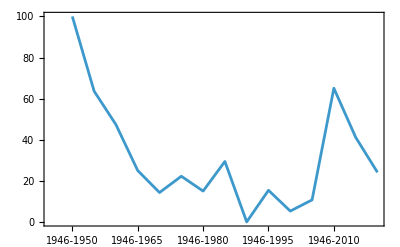
-Graphics-新規出現雑誌の主要雑誌に占める割合（%）

```mathematica
Labeled[ListPlot[top1pcISSNnewcomercount/pivotaljournalcount*100,Joined->True,
Frame->True,FrameTicks->{Automatic,{genticks,None}}],"新規出現雑誌の主要雑誌に占める割合（%）"]
```

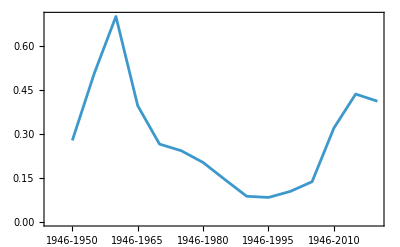
-Graphics-主要雑誌の全雑誌に占める割合（%）

```mathematica
Labeled[ListPlot[pivotaljournalcount/totaljournalcount*100,Joined->True,Frame->True,FrameTicks->{Automatic,{genticks,None}}],"主要雑誌の全雑誌に占める割合（%）"]
```

## 主要雑誌タイトル

```mathematica
top1pcISSN[[1]]
```

{0021-9738,0264-6021,0016-6731,0036-8075,0002-9572}

ISSN vs. journal title
ISSNvsTitle.save

データ

```mathematica
Get["/Volumes/elecom/BANK/pubmed/202312/xml/element/journal-title/ISSNvsTitle.save"]
```

プログラム

```mathematica
Map[ISSNvsTitle,top1pcISSN,{-1}]
```

{{The Journal of clinical investigation,The Biochemical journal,Genetics,Science (New York, N.Y.),American journal of public health and the nation's health},{The Biochemical journal,The Journal of clinical investigation,Science (New York, N.Y.),The Journal of physiology,Genetics,Biochemische Zeitschrift,Journal of bacteriology,The Journal of biological chemistry,Deutsche medizinische Wochenschrift (1946),British journal of pharmacology and chemotherapy,Nature},{The Biochemical journal,The Journal of physiology,The Journal of clinical investigation,The Journal of experimental medicine,The Journal of biological chemistry,Science (New York, N.Y.),The Anatomical record,The Journal of biophysical and biochemical cytology,Journal of cellular and comparative physiology,The journal of histochemistry and cytochemistry : official journal of the Histochemistry Society,British journal of pharmacology and chemotherapy,Archives of biochemistry,The Journal of general physiology,Lancet (London, England),Genetics,Hoppe-Seyler's Zeitschrift fur physiologische Chemie,Journal of bacteriology,Deutsche medizinische Wochenschrift (1946),Nature},{The Biochemical journal,The Journal of biophysical and biochemical cytology,The Journal of biological chemistry,The Journal of physiology,The Journal of experimental medicine,The Journal of cell biology,Journal of bacteriology,The Journal of clinical investigation,Nature,Hoppe-Seyler's Zeitschrift fur physiologische Chemie,Archives of biochemistry,Genetics,Deutsche medizinische Wochenschrift (1946),British journal of experimental pathology,International archives of allergy and applied immunology,Journal of molecular biology},{The Biochemical journal,The Journal of biophysical and biochemical cytology,The Journal of experimental medicine,The Journal of cell biology,The Journal of biological chemistry,The Journal of physiology,Nature,Annals of the New York Academy of Sciences,The Journal of clinical investigation,Science (New York, N.Y.),Journal of bacteriology,Experimental cell research,Journal of molecular biology,International archives of allergy and applied immunology},{The Journal of biological chemistry,The Journal of cell biology,The Biochemical journal,The Journal of biophysical and biochemical cytology,Nature,The Journal of experimental medicine,Journal of immunology (Baltimore, Md. : 1950),The Journal of clinical investigation,Plant physiology,Virology,The Journal of physiology,Journal of molecular biology,Experimental cell research,Journal of bacteriology,Science (New York, N.Y.),Immunochemistry,International archives of allergy and applied immunology,Annals of the New York Academy of Sciences},{The Journal of biological chemistry,The Journal of cell biology,The Journal of experimental medicine,The Biochemical journal,The Journal of biophysical and biochemical cytology,Experimental cell research,European journal of biochemistry,Journal of molecular biology,Bacteriological reviews,Virology,Journal of ultrastructure research,Plant physiology,The Journal of physiology,Science (New York, N.Y.),Journal of bacteriology,The journal of histochemistry and cytochemistry : official journal of the Histochemistry Society,International archives of allergy and applied immunology,Immunochemistry,Annals of the New York Academy of Sciences,Nature},{The Journal of biological chemistry,Proceedings of the National Academy of Sciences of the United States of America,Journal of molecular biology,Biochemistry,Journal of ultrastructure research,The journal of histochemistry and cytochemistry : official journal of the Histochemistry Society,Plant physiology,Nucleic acids research,Immunochemistry,European journal of biochemistry,Annals of the New York Academy of Sciences,The Biochemical journal,Analytical biochemistry,Methods in enzymology,The Journal of biophysical and biochemical cytology,The Journal of cell biology,Nature},{The Journal of biological chemistry,Proceedings of the National Academy of Sciences of the United States of America,Analytical biochemistry,Journal of molecular biology,Annals of the New York Academy of Sciences,The Biochemical journal,The Journal of biophysical and biochemical cytology,Biochemistry,Nucleic acids research,The Journal of cell biology,Methods in enzymology,Nature},{The Journal of biological chemistry,Analytical biochemistry,Proceedings of the National Academy of Sciences of the United States of America,Nucleic acids research,Journal of molecular biology,The Journal of biophysical and biochemical cytology,Pflugers Archiv : European journal of physiology,Science (New York, N.Y.),Gene,The Journal of cell biology,Biochemistry,Methods in enzymology,Nature},{Journal of molecular biology,Proceedings of the National Academy of Sciences of the United States of America,The Journal of biological chemistry,Nucleic acids research,Analytical biochemistry,Journal of bacteriology,European journal of biochemistry,Annals of the New York Academy of Sciences,The Biochemical journal,The Journal of biophysical and biochemical cytology,Virology,Molecular and cellular biology,Science (New York, N.Y.),Pflugers Archiv : European journal of physiology,The Journal of cell biology,Gene,Biochemistry,Methods in enzymology,Nature},{Proceedings of the National Academy of Sciences of the United States of America,Nucleic acids research,Journal of molecular biology,Analytical biochemistry,The Journal of biological chemistry,Gene,Methods in enzymology,The journal of histochemistry and cytochemistry : official journal of the Histochemistry Society,Journal of bacteriology,Science (New York, N.Y.),Nature,Acta crystallographica. Section A, Foundations of crystallography,Journal of ultrastructure research,Scandinavian journal of clinical and laboratory investigation. Supplementum,The Journal of physiology,Immunochemistry,Plant physiology,European journal of biochemistry,Genetics,Molecular biology and evolution,The Biochemical journal,Annals of the New York Academy of Sciences,The Journal of biophysical and biochemical cytology,Virology,Molecular and cellular biology,Pflugers Archiv : European journal of physiology,The Journal of cell biology,Biochemistry},{Proceedings of the National Academy of Sciences of the United States of America,Nature,Journal of molecular biology,Nucleic acids research,Analytical biochemistry,Gene,The Journal of biological chemistry,Science (New York, N.Y.),Cell,Methods in enzymology,Bioinformatics (Oxford, England),Acta crystallographica. Section D, Biological crystallography,CA: a cancer journal for clinicians,Nucleic acids research,Nature,Computer applications in the biosciences : CABIOS,The New England journal of medicine,Journal of molecular graphics,JAMA,The EMBO journal,The journal of histochemistry and cytochemistry : official journal of the Histochemistry Society,Arthritis and rheumatism,European journal of biochemistry,The Biochemical journal,Lancet (London, England),Journal of bacteriology,Molecular and cellular biology,Genetics,Molecular biology and evolution,The Journal of cell biology,Biochemistry,Acta crystallographica. Section A, Foundations of crystallography,Microbiological reviews,Biostatistics (Oxford, England),Journal of the National Cancer Institute,Genome research,JAMA,Yeast (Chichester, England),Journal of chronic diseases,Acta psychiatrica Scandinavica,Archives of biochemistry and biophysics,Journal of molecular and applied genetics,Genome biology,Annual review of biochemistry,Biochemical and biophysical research communications,Systematic biology,Journal of clinical microbiology,Genomics,Development (Cambridge, England),Biochemical pharmacology,Diabetologia,Electrophoresis,Journal of neurology, neurosurgery, and psychiatry,Journal of personality and social psychology,Archives of general psychiatry,Journal of molecular evolution,Pharmacological reviews,Biopolymers,Clinical chemistry,Biometrics,Methods in molecular biology (Clifton, N.J.),Journal of ultrastructure research,Journal of biomolecular NMR,Evolution; international journal of organic evolution,Neuropsychologia,Scandinavian journal of clinical and laboratory investigation. Supplementum,Immunochemistry,Neurology,Briefings in bioinformatics,The Plant journal : for cell and molecular biology,Plant physiology,Medical care,The Journal of physiology,Acta crystallographica. Section D, Biological crystallography,Journal of immunological methods,Annals of the New York Academy of Sciences,The Journal of biophysical and biochemical cytology,Nature genetics,Virology,Journal of psychiatric research,Methods (San Diego, Calif.),Methods in enzymology,Pflugers Archiv : European journal of physiology},{Nature,Proceedings of the National Academy of Sciences of the United States of America,Cell,Journal of molecular biology,Nucleic acids research,Nature,Science (New York, N.Y.),Analytical biochemistry,Genome research,The Journal of biological chemistry,The New England journal of medicine,Bioinformatics (Oxford, England),Acta crystallographica. Section D, Biological crystallography,Genome biology,Bioinformatics (Oxford, England),Nucleic acids research,CA: a cancer journal for clinicians,Nature methods,Genetics,CA: a cancer journal for clinicians,Gene,Methods in enzymology,Acta crystallographica. Section D, Biological crystallography,Science (New York, N.Y.),JAMA,Cell,Nature genetics,Molecular biology and evolution,Psychological bulletin,Biochemical pharmacology,Acta neuropathologica,NeuroImage,Journal of bacteriology,The New England journal of medicine,Archives of general psychiatry,Journal of the National Cancer Institute,Journal of personality and social psychology,Arthritis and rheumatism,Journal of computational chemistry,Journal of molecular graphics,Medical care,BMJ (Clinical research ed.),Biometrics,Controlled clinical trials,Nature protocols,Lancet (London, England),Molecular biology and evolution,Acta crystallographica. Section A, Foundations of crystallography,British journal of cancer,Genomics,Magnetic resonance in medicine,Nature reviews. Neuroscience,European journal of cancer (Oxford, England : 1990),Analytical chemistry,Annual review of biochemistry,Developmental dynamics : an official publication of the American Association of Anatomists,Genome research,Applied and environmental microbiology,Journal of health and social behavior,Annual review of neuroscience,Journal of autism and developmental disorders,Health policy (Amsterdam, Netherlands),Radiology,Nature reviews. Genetics,Journal of clinical microbiology,Pharmacological reviews,Trends in genetics : TIG,Yeast (Chichester, England),Evolutionary bioinformatics online,Journal of ultrastructure research,Nature biotechnology,Schizophrenia bulletin,Psychiatry research,BMC genomics,Physical review. B, Condensed matter,Immunochemistry,Computer applications in the biosciences : CABIOS,British journal of addiction,Nephron,Journal of general internal medicine,American journal of kidney diseases : the official journal of the National Kidney Foundation,Scandinavian journal of clinical and laboratory investigation. Supplementum,Archives of biochemistry and biophysics,The journal of histochemistry and cytochemistry : official journal of the Histochemistry Society,Critical care medicine,BMC evolutionary biology,Diabetes care,Hypertension (Dallas, Tex. : 1979),Computers and biomedical research, an international journal,JAMA,The Journal of clinical psychiatry,The journal of physical chemistry. B,Electrophoresis,Annals of internal medicine,Development (Cambridge, England),European journal of biochemistry,Spatial vision,World Health Organization technical report series,The Biochemical journal,Biopolymers,Plant physiology,Circulation,The EMBO journal,The Journal of biophysical and biochemical cytology,Annals of the New York Academy of Sciences,Briefings in bioinformatics,Journal of molecular evolution,Statistics in medicine,Molecular and cellular biology,The Journal of physiology,Virology,International journal of cancer,Biostatistics (Oxford, England),Journal of neurology, neurosurgery, and psychiatry,Acta psychiatrica Scandinavica,Systematic biology,Statistical applications in genetics and molecular biology,Clinical chemistry,Journal of biomolecular NMR,Evolution; international journal of organic evolution,Journal of applied crystallography,Methods in molecular biology (Clifton, N.J.),Neurology,Diabetologia,The Plant journal : for cell and molecular biology,Journal of immunological methods,Journal of chronic diseases,BMJ (Clinical research ed.),The Journal of cell biology,Neuropsychologia,Biochemistry,Pflugers Archiv : European journal of physiology,American journal of human genetics,Methods in enzymology,Journal of psychiatric research,Methods (San Diego, Calif.)},{Bioinformatics (Oxford, England),CA: a cancer journal for clinicians,Nature,Proceedings of the National Academy of Sciences of the United States of America,Nucleic acids research,The New England journal of medicine,Cell,Genome biology,Nucleic acids research,Journal of molecular biology,Nature,Nature methods,Bioinformatics (Oxford, England),Acta crystallographica. Section D, Biological crystallography,Science (New York, N.Y.),Genome research,Analytical biochemistry,The Journal of biological chemistry,NeuroImage,Science (New York, N.Y.),Nature biotechnology,Genetics,Lancet (London, England),Molecular biology and evolution,Acta crystallographica. Section D, Biological crystallography,Cell,BMC bioinformatics,JAMA,CA: a cancer journal for clinicians,JAMA,Biometrics,Molecular biology and evolution,BMJ (Clinical research ed.),Nature protocols,Acta neuropathologica,Circulation,The New England journal of medicine,Applied and environmental microbiology,Systematic biology,Psychological bulletin,Journal of the National Cancer Institute,Archives of general psychiatry,Annals of internal medicine,Journal of personality and social psychology,Medical care,International journal of cancer,Lancet (London, England),Controlled clinical trials,Journal of computational chemistry,Nature genetics,Acta crystallographica. Section A, Foundations of crystallography,Acta crystallographica. Section C, Structural chemistry,Developmental dynamics : an official publication of the American Association of Anatomists,Sleep,Virology,Systematic reviews,Molecular cell,International journal for quality in health care : journal of the International Society for Quality in Health Care,The EMBO journal,Hypertension (Dallas, Tex. : 1979),American journal of kidney diseases : the official journal of the National Kidney Foundation,Magnetic resonance in medicine,Radiology,Archives of biochemistry and biophysics,Trends in genetics : TIG,Development (Cambridge, England),Plant physiology,BMC evolutionary biology,Diabetes care,Human brain mapping,Nature reviews. Cancer,The Journal of clinical investigation,Critical care medicine,Journal of the American Geriatrics Society,Journal of computational chemistry,British journal of addiction,The journal of physical chemistry. B,Biopolymers,The European respiratory journal,Clinical chemistry,Nature cell biology,Medicine and science in sports and exercise,Nature reviews. Genetics,The Journal of physiology,Annals of internal medicine,Schizophrenia bulletin,Health policy (Amsterdam, Netherlands),Computers and biomedical research, an international journal,The journals of gerontology. Series A, Biological sciences and medical sciences,Journal of neuroscience methods,Nature genetics,Genetics in medicine : official journal of the American College of Medical Genetics,Science signaling,Qualitative health research,Molecular ecology,Molecular systems biology,Physical review. B, Condensed matter,Cytotherapy,Cancer discovery,Journal of molecular evolution,Journal of health and social behavior,BMC genomics,Biostatistics (Oxford, England),Systematic biology,World Health Organization technical report series,Methods in molecular biology (Clifton, N.J.),Spatial vision,Arthritis and rheumatism,The Journal of clinical psychiatry,Psychiatry research,Statistical applications in genetics and molecular biology,Applied and environmental microbiology,Annals of surgery,Biochemistry,Journal of biomolecular NMR,Journal of neurology, neurosurgery, and psychiatry,Physical review letters,The Journal of cell biology,Pflugers Archiv : European journal of physiology,Journal of computational biology : a journal of computational molecular cell biology,Clinical chemistry,Behavior research methods,Evolution; international journal of organic evolution,Methods in enzymology,Gene,Neurology,Journal of general internal medicine,European journal of cancer (Oxford, England : 1990),Statistics in medicine,Journal of biomedical informatics,Genome research,The Plant journal : for cell and molecular biology,Diabetologia,Journal of immunological methods,Acta psychiatrica Scandinavica,Journal of applied crystallography,Neuropsychologia,Journal of molecular graphics,PLoS medicine,Journal of chronic diseases,American journal of human genetics,Methods in enzymology,BMJ (Clinical research ed.),Journal of psychiatric research,Methods (San Diego, Calif.)}}